```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/andrei/Work/physics/B-physics/BcBcNLO/calc/BcBc/VV/west/gamma/renorm

```mathematica
PrependTo[$Path,"/home/andrei/Work/physics/B-physics/BcBcNLO/calc/pkg"];
```

```mathematica
<<X`
```

Package-X v1.0.4, by Hiren H. Patel

For more information, see the

```mathematica
NumericQ[r]=True;
```

```mathematica
PackageXSubs={LDot[p3,p3]->m^2,LDot[p4,p4]->m^2,LDot[p3,p4]->s/2-m^2,mc-> r m, mb-> (1-r) m};
```

```mathematica
toABC={pvA[a_,b_]:>A[b],pvB[a_,b_,c___]:>B[c],pvC[a_,b_,c_,d___]:>C[d],pvC0[a__]:>C[a]};
topvABC={A[a_]:>pvA[0,a],B[a__]:>pvB[0,0,a],C[a__]:>pvC[0,0,0,a]};
```

```mathematica
factor=(Exp[EulerGamma] 1/(4 Pi))^-eps
```

ⅇ^(ℽ (-eps)) (4 π)^eps

```mathematica
ff=Gamma[1-2 eps]/(Gamma[1-eps]^2 Gamma[1+eps](4 Pi)^eps I/(16 Pi^2))
```

-(ⅈ (4 π)^(2-eps) 1-2 eps)/((1-eps)^2 eps+1)

```mathematica
invff=1/ff
```

(ⅈ (4 π)^(eps-2) (1-eps)^2 eps+1)/(1-2 eps)

```mathematica
Normal[Series[FullSimplify[1/factor invff],{eps,0,1}]]
```

ⅈ/(16 π^2)

```mathematica
norm=Expand[Normal[Series[FullSimplify[1/factor invff],{eps,0,2}]]/(I/(16 Pi^2))]
```

1-(π^2 eps^2)/12

```mathematica
Fb=(((1-r)^2 m^2)/mmu)^-eps
```

((m^2 (1-r)^2)/mmu)^-eps

```mathematica
Fc=((r^2 m^2)/mmu)^-eps
```

((m^2 r^2)/mmu)^-eps

```mathematica
Fb=Plus@@ Factor[List@@ Normal[Series[Fb,{eps,0,1}]]/.{Log[(m^2 (1-r)^2)/mmu]->Log[m^2/mmu]+ 2 Log[1-r]}]
```

1-eps (log(m^2/mmu)+2 log(1-r))

```mathematica
Fc=Plus@@ Factor[List@@ Normal[Series[Fc,{eps,0,1}]]/.{Log[(m^2 r^2)/mmu]->Log[m^2/mmu]+ 2 Log[r]}]
```

1-eps (log(m^2/mmu)+2 log(r))

```mathematica
A0[m_]:=m^2+m^2/eps+eps*m^2+(eps*m^2*Pi^2)/6+m^2*Log[mmu/m^2]+eps*m^2*Log[mmu/m^2]+(eps*m^2*Log[mmu/m^2]^2)/2
```

```mathematica
F21[z_]:=(1-eps)/(2 (1-2 eps) z)(1+z-(1-z)^(1-2 eps)-2 (1-z)^(1-2 eps) eps (eps PolyLog[1,1,z]+Hui eps^2 Sum[(-2)^(j-k) PolyLog[k,3-k],{k,1,2}]))
```

```mathematica
B0polylog[s_,m1_,m2_]:=Block[{x,y,lam},If[m1≠ 0 && m2≠0,x=m1^2/s;y=m2^2/s;lam=√((1-x-y)^2-4 x y);  mmu^eps(I Pi^(2-eps))/(2 Pi)^(4-2 eps) (-s)^-eps ((Gamma[1-eps]^2 Gamma[eps])/Gamma[2-2 eps] lam^(1- 2 eps)-Gamma[-1+eps] 1/2(1+x-y-lam) (-x)^-eps F21[(1+x-y-lam)^2/(4 x)]-
Gamma[-1+eps] 1/2(1-x+y-lam) (-y)^-eps F21[(1-x+y-lam)^2/(4 y)]),If[m1==0 && m2 ≠ 0,mmu^eps(I Pi^(2-eps))/(2 Pi)^(4-2 eps) m2^(-2 eps) Gamma[1+eps]/(eps (1-eps))F21[s/m2^2],If[m1≠ 0 && m2== 0,mmu^eps(I Pi^(2-eps))/(2 Pi)^(4-2 eps) m1^(-2 eps) Gamma[1+eps]/(eps (1-eps))F21[s/m1^2],If[m1==0 && m2==0,mmu^eps(I Pi^(2-eps))/(2 Pi)^(4-2 eps) (-s)^-eps (Gamma[1-eps]^2 Gamma[eps])/Gamma[2-2 eps]]]]]]
```

```mathematica
<<cross-sectionNLOWest.res
```

```mathematica
(* X[a_]:=norm *)
```

```mathematica
mc=1.5;mb=4.9;m=mc+mb;r=mc/m;CF=4/3;CA=3;pi=Pi;s=15^2;mt=175;R1=R2=1;nf=6;AL=1/137;
```

```mathematica
Sqrt[4 m^2]
```

12.8

```mathematica
(2mc+2 mc)^2
```

36.

```mathematica
pow[a_,b_]:=a^b
```

```mathematica
(* AS=0.3; mmu=(2 m)^2; *)
```

```mathematica
ex[1]=Collect[Expand[crosssection//N],{A[___],B[___],C[___]}]
```

6.10514×10^-12 eps Aconj(1.5) AS^3-(7.266×10^-13 Aconj(1.5) AS^3)/eps+3.26835×10^-11 Aconj(1.5) AS^3-4.33974×10^-12 eps Aconj(4.9) AS^3+(2.22428×10^-13 Aconj(4.9) AS^3)/eps+2.04951×10^-11 Aconj(4.9) AS^3-2.81937×10^-13 eps Aconj(175.) AS^3+8.48466×10^-13 Aconj(175.) AS^3-5.25678×10^-10 eps Bconj(12.3596,0.,0.) AS^3+3.86578×10^-10 Bconj(12.3596,0.,0.) AS^3+5.90179×10^-13 eps Bconj(12.3596,1.5,1.5) AS^3+(6.47124×10^-12 Bconj(12.3596,1.5,1.5) AS^3)/eps-1.66452×10^-11 Bconj(12.3596,1.5,1.5) AS^3-1.12936×10^-11 eps Bconj(12.3596,4.9,4.9) AS^3-3.34242×10^-11 Bconj(12.3596,4.9,4.9) AS^3-1.7249×10^-8 eps Bconj(12.3596,175.,175.) AS^3-2.58414×10^-8 Bconj(12.3596,175.,175.) AS^3+2.12954×10^-10 eps Bconj(51.9348,1.5,4.9) AS^3-(8.32407×10^-12 Bconj(51.9348,1.5,4.9) AS^3)/eps-1.53731×10^-10 Bconj(51.9348,1.5,4.9) AS^3-1.95933×10^-10 eps Bconj(51.9348,4.9,1.5) AS^3-(8.32407×10^-12 Bconj(51.9348,4.9,1.5) AS^3)/eps+1.73706×10^-10 Bconj(51.9348,4.9,1.5) AS^3+5.10325×10^-10 eps Bconj(76.7444,0.,4.9) AS^3-3.60532×10^-10 Bconj(76.7444,0.,4.9) AS^3+6.16262×10^-10 eps Bconj(76.7444,4.9,0.) AS^3-4.32622×10^-10 Bconj(76.7444,4.9,0.) AS^3-6.94312×10^-11 eps Bconj(131.891,0.,0.) AS^3+2.58825×10^-10 Bconj(131.891,0.,0.) AS^3+2.25022×10^-12 eps Bconj(131.891,1.5,1.5) AS^3+1.77468×10^-13 Bconj(131.891,1.5,1.5) AS^3-1.8977×10^-12 eps Bconj(131.891,4.9,4.9) AS^3+(6.47124×10^-12 Bconj(131.891,4.9,4.9) AS^3)/eps-3.00357×10^-12 Bconj(131.891,4.9,4.9) AS^3-9.90684×10^-11 eps Bconj(131.891,175.,175.) AS^3-1.48378×10^-10 Bconj(131.891,175.,175.) AS^3+1.36283×10^-10 eps Bconj(174.516,0.,1.5) AS^3-4.12726×10^-10 Bconj(174.516,0.,1.5) AS^3+1.77802×10^-11 eps Bconj(174.516,1.5,0.) AS^3-4.18817×10^-11 Bconj(174.516,1.5,0.) AS^3-8.85713×10^-11 eps Bconj(225.,1.5,1.5) AS^3+1.84249×10^-10 Bconj(225.,1.5,1.5) AS^3-2.16835×10^-10 eps Bconj(225.,4.9,4.9) AS^3+5.9485×10^-11 Bconj(225.,4.9,4.9) AS^3+1.98603×10^-10 eps Cconj(2.25,12.3596,2.25,0.,1.5,0.) AS^3-7.68017×10^-11 Cconj(2.25,12.3596,2.25,0.,1.5,0.) AS^3-2.76069×10^-9 eps Cconj(2.25,76.7444,40.96,4.9,1.5,0.) AS^3+1.19804×10^-9 Cconj(2.25,76.7444,40.96,4.9,1.5,0.) AS^3-7.32366×10^-11 eps Cconj(2.25,76.7444,51.9348,4.9,1.5,0.) AS^3-2.8177×10^-11 Cconj(2.25,76.7444,51.9348,4.9,1.5,0.) AS^3+1.47418×10^-10 eps Cconj(2.25,131.891,174.516,0.,1.5,0.) AS^3-7.4273×10^-10 Cconj(2.25,131.891,174.516,0.,1.5,0.) AS^3-2.13932×10^-11 eps Cconj(2.25,174.516,131.891,1.5,1.5,0.) AS^3-1.85978×10^-11 Cconj(2.25,174.516,131.891,1.5,1.5,0.) AS^3-2.00753×10^-9 eps Cconj(2.25,174.516,225.,1.5,1.5,0.) AS^3+3.39×10^-9 Cconj(2.25,174.516,225.,1.5,1.5,0.) AS^3+5.63782×10^-9 eps Cconj(24.01,12.3596,76.7444,0.,4.9,0.) AS^3-4.0071×10^-9 Cconj(24.01,12.3596,76.7444,0.,4.9,0.) AS^3-1.4802×10^-11 eps Cconj(24.01,76.7444,12.3596,4.9,4.9,0.) AS^3+2.49743×10^-10 Cconj(24.01,76.7444,12.3596,4.9,4.9,0.) AS^3+2.62843×10^-10 eps Cconj(24.01,76.7444,225.,4.9,4.9,0.) AS^3-1.89446×10^-9 Cconj(24.01,76.7444,225.,4.9,4.9,0.) AS^3+3.03311×10^-10 eps Cconj(24.01,131.891,24.01,0.,4.9,0.) AS^3+9.19125×10^-10 Cconj(24.01,131.891,24.01,0.,4.9,0.) AS^3-5.52261×10^-10 eps Cconj(24.01,174.516,40.96,1.5,4.9,0.) AS^3-8.0561×10^-10 Cconj(24.01,174.516,40.96,1.5,4.9,0.) AS^3+3.84155×10^-11 eps Cconj(24.01,174.516,51.9348,1.5,4.9,0.) AS^3-2.29215×10^-11 Cconj(24.01,174.516,51.9348,1.5,4.9,0.) AS^3-2.05463×10^-10 eps Cconj(51.9348,51.9348,225.,1.5,1.5,4.9) AS^3+2.67628×10^-11 Cconj(51.9348,51.9348,225.,1.5,1.5,4.9) AS^3-7.32366×10^-11 eps Cconj(76.7444,2.25,51.9348,1.5,4.9,0.) AS^3-2.8177×10^-11 Cconj(76.7444,2.25,51.9348,1.5,4.9,0.) AS^3+5.23148×10^-9 eps Cconj(76.7444,12.3596,24.01,0.,4.9,0.) AS^3-3.91683×10^-9 Cconj(76.7444,12.3596,24.01,0.,4.9,0.) AS^3-1.4802×10^-11 eps Cconj(76.7444,24.01,12.3596,4.9,4.9,0.) AS^3+2.49743×10^-10 Cconj(76.7444,24.01,12.3596,4.9,4.9,0.) AS^3-7.0217×10^-9 eps Cconj(76.7444,24.01,225.,4.9,4.9,0.) AS^3+1.63401×10^-9 Cconj(76.7444,24.01,225.,4.9,4.9,0.) AS^3-2.13932×10^-11 eps Cconj(174.516,2.25,131.891,1.5,1.5,0.) AS^3-1.85978×10^-11 Cconj(174.516,2.25,131.891,1.5,1.5,0.) AS^3+3.84155×10^-11 eps Cconj(174.516,24.01,51.9348,4.9,1.5,0.) AS^3-2.29215×10^-11 Cconj(174.516,24.01,51.9348,4.9,1.5,0.) AS^3+1.50631×10^-9 eps Cconj(174.516,131.891,2.25,0.,1.5,0.) AS^3-3.75684×10^-9 Cconj(174.516,131.891,2.25,0.,1.5,0.) AS^3+3.19458×10^-12 eps Cconj(225.,51.9348,51.9348,1.5,4.9,4.9) AS^3+2.02675×10^-10 Cconj(225.,51.9348,51.9348,1.5,4.9,4.9) AS^3+1.33792×10^-10 log(0.234375) AS^3+2.9322×10^-10 log(0.765625) AS^3-2.13506×10^-10 log(0.0244141 mmu) AS^3-(3.29684×10^-10 AS^3)/eps-2.85021×10^-10 AS^3+1.04281×10^-10 AS^2+(6.10514×10^-12 eps AS^3-(7.266×10^-13 AS^3)/eps+3.26835×10^-11 AS^3) A(1.5)+(-4.33974×10^-12 eps AS^3+(2.22428×10^-13 AS^3)/eps+2.04951×10^-11 AS^3) A(4.9)+(8.48466×10^-13 AS^3-2.81937×10^-13 AS^3 eps) A(175.)+(3.86578×10^-10 AS^3-5.25678×10^-10 AS^3 eps) B(12.3596,0.,0.)+(5.90179×10^-13 eps AS^3+(6.47124×10^-12 AS^3)/eps-1.66452×10^-11 AS^3) B(12.3596,1.5,1.5)+(-1.12936×10^-11 eps AS^3-3.34242×10^-11 AS^3) B(12.3596,4.9,4.9)+(-1.7249×10^-8 eps AS^3-2.58414×10^-8 AS^3) B(12.3596,175.,175.)+(2.12954×10^-10 eps AS^3-(8.32407×10^-12 AS^3)/eps-1.53731×10^-10 AS^3) B(51.9348,1.5,4.9)+(-1.95933×10^-10 eps AS^3-(8.32407×10^-12 AS^3)/eps+1.73706×10^-10 AS^3) B(51.9348,4.9,1.5)+(5.10325×10^-10 AS^3 eps-3.60532×10^-10 AS^3) B(76.7444,0.,4.9)+(6.16262×10^-10 AS^3 eps-4.32622×10^-10 AS^3) B(76.7444,4.9,0.)+(2.58825×10^-10 AS^3-6.94312×10^-11 AS^3 eps) B(131.891,0.,0.)+(2.25022×10^-12 eps AS^3+1.77468×10^-13 AS^3) B(131.891,1.5,1.5)+(-1.8977×10^-12 eps AS^3+(6.47124×10^-12 AS^3)/eps-3.00357×10^-12 AS^3) B(131.891,4.9,4.9)+(-9.90684×10^-11 eps AS^3-1.48378×10^-10 AS^3) B(131.891,175.,175.)+(1.36283×10^-10 AS^3 eps-4.12726×10^-10 AS^3) B(174.516,0.,1.5)+(1.77802×10^-11 AS^3 eps-4.18817×10^-11 AS^3) B(174.516,1.5,0.)+(1.84249×10^-10 AS^3-8.85713×10^-11 AS^3 eps) B(225.,1.5,1.5)+(5.9485×10^-11 AS^3-2.16835×10^-10 AS^3 eps) B(225.,4.9,4.9)+(1.98603×10^-10 AS^3 eps-7.68017×10^-11 AS^3) C[2.25,12.3596,2.25,0,1.5,0]+(1.19804×10^-9 AS^3-2.76069×10^-9 AS^3 eps) C[2.25,76.7444,40.96,4.9,1.5,0]+(-7.32366×10^-11 eps AS^3-2.8177×10^-11 AS^3) C[2.25,76.7444,51.9348,4.9,1.5,0]+(1.47418×10^-10 AS^3 eps-7.4273×10^-10 AS^3) C[2.25,131.891,174.516,0,1.5,0]+(-2.13932×10^-11 eps AS^3-1.85978×10^-11 AS^3) C[2.25,174.516,131.891,1.5,1.5,0]+(3.39×10^-9 AS^3-2.00753×10^-9 AS^3 eps) C[2.25,174.516,225,1.5,1.5,0]+(5.63782×10^-9 AS^3 eps-4.0071×10^-9 AS^3) C[24.01,12.3596,76.7444,0,4.9,0]+(2.49743×10^-10 AS^3-1.4802×10^-11 AS^3 eps) C[24.01,76.7444,12.3596,4.9,4.9,0]+(2.62843×10^-10 AS^3 eps-1.89446×10^-9 AS^3) C[24.01,76.7444,225,4.9,4.9,0]+(3.03311×10^-10 eps AS^3+9.19125×10^-10 AS^3) C[24.01,131.891,24.01,0,4.9,0]+(-5.52261×10^-10 eps AS^3-8.0561×10^-10 AS^3) C[24.01,174.516,40.96,1.5,4.9,0]+(3.84155×10^-11 AS^3 eps-2.29215×10^-11 AS^3) C[24.01,174.516,51.9348,1.5,4.9,0]+(2.67628×10^-11 AS^3-2.05463×10^-10 AS^3 eps) C[51.9348,51.9348,225,1.5,1.5,4.9]+(-7.32366×10^-11 eps AS^3-2.8177×10^-11 AS^3) C[76.7444,2.25,51.9348,1.5,4.9,0]+(5.23148×10^-9 AS^3 eps-3.91683×10^-9 AS^3) C[76.7444,12.3596,24.01,0,4.9,0]+(2.49743×10^-10 AS^3-1.4802×10^-11 AS^3 eps) C[76.7444,24.01,12.3596,4.9,4.9,0]+(1.63401×10^-9 AS^3-7.0217×10^-9 AS^3 eps) C[76.7444,24.01,225,4.9,4.9,0]+(-2.13932×10^-11 eps AS^3-1.85978×10^-11 AS^3) C[174.516,2.25,131.891,1.5,1.5,0]+(3.84155×10^-11 AS^3 eps-2.29215×10^-11 AS^3) C[174.516,24.01,51.9348,4.9,1.5,0]+(1.50631×10^-9 AS^3 eps-3.75684×10^-9 AS^3) C[174.516,131.891,2.25,0,1.5,0]+(3.19458×10^-12 eps AS^3+2.02675×10^-10 AS^3) C[225,51.9348,51.9348,1.5,4.9,4.9]

```mathematica
Bconj[s,0.,0.]/.{Bconj[s_,0.,0.]:> Expand[ExpandAll[Conjugate[FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,0,0] ,{eps,0,1}]]]]]/.{Conjugate[eps]-> eps,Conjugate[Log[mmu]]-> Log[mmu],Conjugate[eps Log[mmu]]-> eps Log[mmu]}]}
```

-(3.4161+3.14159 ⅈ) eps log(mmu)+(2.90007+10.732 ⅈ) eps-(3.4161+3.14159 ⅈ)+0.5 eps log^2(mmu)+1/eps+log(mmu)

```mathematica
ex[2]=Expand[Simplify[Normal[Series[ex[1]/.{A[m_]:> A0[m],B[s_,0.,0.]:> FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,0,0] ,{eps,0,1}]]],B[s_,m_,0.]:> FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,m,0] ,{eps,0,1}]]],B[s_,0.,m_]:> FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,0,m] ,{eps,0,1}]]],B[s_,m1_,m2_]:> FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,m1,m2] ,{eps,0,1}]]],Aconj[m_]:> Conjugate[A0[m]],Bconj[s_,0.,0.]:> Conjugate[FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,0,0] ,{eps,0,1}]]]],Bconj[s_,m_,0.]:> Conjugate[FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,m,0] ,{eps,0,1}]]]],Bconj[s_,0.,m_]:> Conjugate[FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,0,m] ,{eps,0,1}]]]],Bconj[s_,m1_,m2_]:> Conjugate[FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,m1,m2] ,{eps,0,1}]]]],log[a_]:>  Log[a]},{eps,0,0}]]/.{Log[a_ mmu]-> Log[a]+Log[mmu]}]/.{Conjugate[eps]-> eps,Conjugate[Log[mmu]]-> Log[mmu],Conjugate[eps Log[mmu]]-> eps Log[mmu]}]
```

(-1.3476×10^-6+1.50881×10^-9 ⅈ) eps^2 AS^3-(1.28431×10^-8-2.45111×10^-22 ⅈ) eps^2 log^2(mmu) AS^3+(1.68548×10^-10-2.1412×10^-27 ⅈ) eps log^2(mmu) AS^3+(1.0259×10^-25-1.49144×10^-31 ⅈ) log^2(mmu) AS^3+(3.44357×10^-8+1.44757×10^-24 ⅈ) eps AS^3+1.98603×10^-10 eps C[2.25,12.3596,2.25,0,1.5,0] AS^3-(7.68017×10^-11-2.52435×10^-29 ⅈ) C[2.25,12.3596,2.25,0,1.5,0] AS^3-(2.76069×10^-9-3.23117×10^-27 ⅈ) eps C[2.25,76.7444,40.96,4.9,1.5,0] AS^3+(1.19804×10^-9-4.03897×10^-28 ⅈ) C[2.25,76.7444,40.96,4.9,1.5,0] AS^3-(7.32366×10^-11-2.52435×10^-29 ⅈ) eps C[2.25,76.7444,51.9348,4.9,1.5,0] AS^3-(2.8177×10^-11-1.26218×10^-29 ⅈ) C[2.25,76.7444,51.9348,4.9,1.5,0] AS^3+(1.47418×10^-10-1.51461×10^-28 ⅈ) eps C[2.25,131.891,174.516,0,1.5,0] AS^3-(7.4273×10^-10-6.05845×10^-28 ⅈ) C[2.25,131.891,174.516,0,1.5,0] AS^3-(2.13932×10^-11-1.26218×10^-29 ⅈ) eps C[2.25,174.516,131.891,1.5,1.5,0] AS^3-(1.85978×10^-11-1.89327×10^-29 ⅈ) C[2.25,174.516,131.891,1.5,1.5,0] AS^3-(2.00753×10^-9+4.03897×10^-28 ⅈ) eps C[2.25,174.516,225,1.5,1.5,0] AS^3+(3.39×10^-9-2.42338×10^-27 ⅈ) C[2.25,174.516,225,1.5,1.5,0] AS^3+(5.63782×10^-9-3.23117×10^-27 ⅈ) eps C[24.01,12.3596,76.7444,0,4.9,0] AS^3-(4.0071×10^-9-4.03897×10^-27 ⅈ) C[24.01,12.3596,76.7444,0,4.9,0] AS^3-(1.4802×10^-11-6.31089×10^-30 ⅈ) eps C[24.01,76.7444,12.3596,4.9,4.9,0] AS^3+(2.49743×10^-10-1.51461×10^-28 ⅈ) C[24.01,76.7444,12.3596,4.9,4.9,0] AS^3+(2.62843×10^-10-1.00974×10^-28 ⅈ) eps C[24.01,76.7444,225,4.9,4.9,0] AS^3-(1.89446×10^-9-8.07794×10^-28 ⅈ) C[24.01,76.7444,225,4.9,4.9,0] AS^3+(3.03311×10^-10-1.00974×10^-28 ⅈ) eps C[24.01,131.891,24.01,0,4.9,0] AS^3+(9.19125×10^-10-4.03897×10^-28 ⅈ) C[24.01,131.891,24.01,0,4.9,0] AS^3-(5.52261×10^-10-3.02923×10^-28 ⅈ) eps C[24.01,174.516,40.96,1.5,4.9,0] AS^3-(8.0561×10^-10-8.07794×10^-28 ⅈ) C[24.01,174.516,40.96,1.5,4.9,0] AS^3+(3.84155×10^-11-1.26218×10^-29 ⅈ) eps C[24.01,174.516,51.9348,1.5,4.9,0] AS^3-(2.29215×10^-11-2.52435×10^-29 ⅈ) C[24.01,174.516,51.9348,1.5,4.9,0] AS^3-(2.05463×10^-10-5.04871×10^-29 ⅈ) eps C[51.9348,51.9348,225,1.5,1.5,4.9] AS^3+(2.67628×10^-11-3.15544×10^-29 ⅈ) C[51.9348,51.9348,225,1.5,1.5,4.9] AS^3-(7.32366×10^-11-2.52435×10^-29 ⅈ) eps C[76.7444,2.25,51.9348,1.5,4.9,0] AS^3-(2.8177×10^-11-1.26218×10^-29 ⅈ) C[76.7444,2.25,51.9348,1.5,4.9,0] AS^3+(5.23148×10^-9-3.23117×10^-27 ⅈ) eps C[76.7444,12.3596,24.01,0,4.9,0] AS^3-(3.91683×10^-9-2.42338×10^-27 ⅈ) C[76.7444,12.3596,24.01,0,4.9,0] AS^3-(1.4802×10^-11-6.31089×10^-30 ⅈ) eps C[76.7444,24.01,12.3596,4.9,4.9,0] AS^3+(2.49743×10^-10-1.51461×10^-28 ⅈ) C[76.7444,24.01,12.3596,4.9,4.9,0] AS^3-(7.0217×10^-9+7.17465×10^-43 ⅈ) eps C[76.7444,24.01,225,4.9,4.9,0] AS^3+(1.63401×10^-9-1.21169×10^-27 ⅈ) C[76.7444,24.01,225,4.9,4.9,0] AS^3-(2.13932×10^-11-1.26218×10^-29 ⅈ) eps C[174.516,2.25,131.891,1.5,1.5,0] AS^3-(1.85978×10^-11-1.89327×10^-29 ⅈ) C[174.516,2.25,131.891,1.5,1.5,0] AS^3+(3.84155×10^-11-1.26218×10^-29 ⅈ) eps C[174.516,24.01,51.9348,4.9,1.5,0] AS^3-(2.29215×10^-11-2.52435×10^-29 ⅈ) C[174.516,24.01,51.9348,4.9,1.5,0] AS^3+(1.50631×10^-9-4.03897×10^-28 ⅈ) eps C[174.516,131.891,2.25,0,1.5,0] AS^3-(3.75684×10^-9-8.07794×10^-28 ⅈ) C[174.516,131.891,2.25,0,1.5,0] AS^3+(3.19458×10^-12-4.73317×10^-30 ⅈ) eps C[225,51.9348,51.9348,1.5,4.9,4.9] AS^3+(2.02675×10^-10-5.04871×10^-29 ⅈ) C[225,51.9348,51.9348,1.5,4.9,4.9] AS^3+1.98603×10^-10 eps Cconj(2.25,12.3596,2.25,0.,1.5,0.) AS^3-(7.68017×10^-11-2.52435×10^-29 ⅈ) Cconj(2.25,12.3596,2.25,0.,1.5,0.) AS^3-(2.76069×10^-9-3.23117×10^-27 ⅈ) eps Cconj(2.25,76.7444,40.96,4.9,1.5,0.) AS^3+(1.19804×10^-9-4.03897×10^-28 ⅈ) Cconj(2.25,76.7444,40.96,4.9,1.5,0.) AS^3-(7.32366×10^-11-2.52435×10^-29 ⅈ) eps Cconj(2.25,76.7444,51.9348,4.9,1.5,0.) AS^3-(2.8177×10^-11-1.26218×10^-29 ⅈ) Cconj(2.25,76.7444,51.9348,4.9,1.5,0.) AS^3+(1.47418×10^-10-1.51461×10^-28 ⅈ) eps Cconj(2.25,131.891,174.516,0.,1.5,0.) AS^3-(7.4273×10^-10-6.05845×10^-28 ⅈ) Cconj(2.25,131.891,174.516,0.,1.5,0.) AS^3-(2.13932×10^-11-1.26218×10^-29 ⅈ) eps Cconj(2.25,174.516,131.891,1.5,1.5,0.) AS^3-(1.85978×10^-11-1.89327×10^-29 ⅈ) Cconj(2.25,174.516,131.891,1.5,1.5,0.) AS^3-(2.00753×10^-9+4.03897×10^-28 ⅈ) eps Cconj(2.25,174.516,225.,1.5,1.5,0.) AS^3+(3.39×10^-9-2.42338×10^-27 ⅈ) Cconj(2.25,174.516,225.,1.5,1.5,0.) AS^3+(5.63782×10^-9-3.23117×10^-27 ⅈ) eps Cconj(24.01,12.3596,76.7444,0.,4.9,0.) AS^3-(4.0071×10^-9-4.03897×10^-27 ⅈ) Cconj(24.01,12.3596,76.7444,0.,4.9,0.) AS^3-(1.4802×10^-11-6.31089×10^-30 ⅈ) eps Cconj(24.01,76.7444,12.3596,4.9,4.9,0.) AS^3+(2.49743×10^-10-1.51461×10^-28 ⅈ) Cconj(24.01,76.7444,12.3596,4.9,4.9,0.) AS^3+(2.62843×10^-10-1.00974×10^-28 ⅈ) eps Cconj(24.01,76.7444,225.,4.9,4.9,0.) AS^3-(1.89446×10^-9-8.07794×10^-28 ⅈ) Cconj(24.01,76.7444,225.,4.9,4.9,0.) AS^3+(3.03311×10^-10-1.00974×10^-28 ⅈ) eps Cconj(24.01,131.891,24.01,0.,4.9,0.) AS^3+(9.19125×10^-10-4.03897×10^-28 ⅈ) Cconj(24.01,131.891,24.01,0.,4.9,0.) AS^3-(5.52261×10^-10-3.02923×10^-28 ⅈ) eps Cconj(24.01,174.516,40.96,1.5,4.9,0.) AS^3-(8.0561×10^-10-8.07794×10^-28 ⅈ) Cconj(24.01,174.516,40.96,1.5,4.9,0.) AS^3+(3.84155×10^-11-1.26218×10^-29 ⅈ) eps Cconj(24.01,174.516,51.9348,1.5,4.9,0.) AS^3-(2.29215×10^-11-2.52435×10^-29 ⅈ) Cconj(24.01,174.516,51.9348,1.5,4.9,0.) AS^3-(2.05463×10^-10-5.04871×10^-29 ⅈ) eps Cconj(51.9348,51.9348,225.,1.5,1.5,4.9) AS^3+(2.67628×10^-11-3.15544×10^-29 ⅈ) Cconj(51.9348,51.9348,225.,1.5,1.5,4.9) AS^3-(7.32366×10^-11-2.52435×10^-29 ⅈ) eps Cconj(76.7444,2.25,51.9348,1.5,4.9,0.) AS^3-(2.8177×10^-11-1.26218×10^-29 ⅈ) Cconj(76.7444,2.25,51.9348,1.5,4.9,0.) AS^3+(5.23148×10^-9-3.23117×10^-27 ⅈ) eps Cconj(76.7444,12.3596,24.01,0.,4.9,0.) AS^3-(3.91683×10^-9-2.42338×10^-27 ⅈ) Cconj(76.7444,12.3596,24.01,0.,4.9,0.) AS^3-(1.4802×10^-11-6.31089×10^-30 ⅈ) eps Cconj(76.7444,24.01,12.3596,4.9,4.9,0.) AS^3+(2.49743×10^-10-1.51461×10^-28 ⅈ) Cconj(76.7444,24.01,12.3596,4.9,4.9,0.) AS^3-(7.0217×10^-9+7.17465×10^-43 ⅈ) eps Cconj(76.7444,24.01,225.,4.9,4.9,0.) AS^3+(1.63401×10^-9-1.21169×10^-27 ⅈ) Cconj(76.7444,24.01,225.,4.9,4.9,0.) AS^3-(2.13932×10^-11-1.26218×10^-29 ⅈ) eps Cconj(174.516,2.25,131.891,1.5,1.5,0.) AS^3-(1.85978×10^-11-1.89327×10^-29 ⅈ) Cconj(174.516,2.25,131.891,1.5,1.5,0.) AS^3+(3.84155×10^-11-1.26218×10^-29 ⅈ) eps Cconj(174.516,24.01,51.9348,4.9,1.5,0.) AS^3-(2.29215×10^-11-2.52435×10^-29 ⅈ) Cconj(174.516,24.01,51.9348,4.9,1.5,0.) AS^3+(1.50631×10^-9-4.03897×10^-28 ⅈ) eps Cconj(174.516,131.891,2.25,0.,1.5,0.) AS^3-(3.75684×10^-9-8.07794×10^-28 ⅈ) Cconj(174.516,131.891,2.25,0.,1.5,0.) AS^3+(3.19458×10^-12-4.73317×10^-30 ⅈ) eps Cconj(225.,51.9348,51.9348,1.5,4.9,4.9) AS^3+(2.02675×10^-10-5.04871×10^-29 ⅈ) Cconj(225.,51.9348,51.9348,1.5,4.9,4.9) AS^3+(2.58928×10^-7-2.78165×10^-10 ⅈ) eps^2 log(mmu) AS^3+(8.63226×10^-10+2.06795×10^-25 ⅈ) eps log(mmu) AS^3+((2.03564×10^-25-1.56945×10^-43 ⅈ) log(mmu) AS^3)/eps+(1.16178×10^-10+7.9719×10^-28 ⅈ) log(mmu) AS^3-((8.47933×10^-21-5.04871×10^-28 ⅈ) AS^3)/eps+((2.03279×10^-25+4.23628×10^-30 ⅈ) AS^3)/eps^2+(1.1158×10^-9-8.48183×10^-26 ⅈ) AS^3+(1.04281×10^-10-2.52435×10^-29 ⅈ) AS^2

```mathematica
ex[3]=Expand[Chop[LoopRefine[Expand[Normal[Series[ex[2],{eps,0,0}]]/.{Cconj[a___]:> Conjugate[C[a]]}]/.topvABC],10^(-20)]]
```

1.16178×10^-10 AS^3 log(mmu)-3.23788×10^-10 AS^3+1.04281×10^-10 AS^2

```mathematica
ex[4]=Collect[Chop[ex[3],10^(-20)],AS]/.{AS-> z *0.3}//Expand
```

3.13682×10^-12 z^3 log(mmu)-8.74228×10^-12 z^3+9.38533×10^-12 z^2

```mathematica
ratioCrossSection[mu2_]:=Abs[N[Coefficient[ex[4],z^3]/Coefficient[ex[4],z^2]/.{mmu-> mu2}]]
```

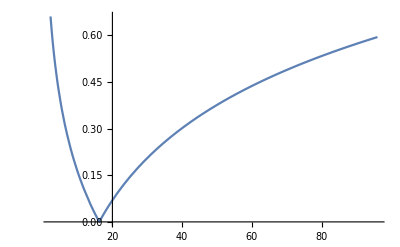

```mathematica
Plot[ratioCrossSection[mmu],{mmu,(mc)^2,(2mb)^2}]
```

```mathematica
ratioCrossSection[(2mc)^2]
```

0.197116

```mathematica
CrossSectionRatio=Abs[N[Coefficient[ex[4],z^3]/Coefficient[ex[4],z^2]]]/.{mmu-> m^2}
```

0.30936

```mathematica
Chop[Expand[ex[4]0.3894 10^12/.{mmu-> (2 mc)^2}],10^(-9)]
```

3.65465 z^2-0.720388 z^3